## NRC Stochastic Volatility:

### Basic specification: NRC and stochastic volatility of inflation

```mathematica
Get["FernandoDuarte`LongRunRisk`"]
```

```mathematica
Keys[Models]
```

{DES,NRCStochVol}

```mathematica
Info[Models]
```

```mathematica
m1=Models["NRCStochVol"];
m1["params"]
```

{delta→0.99,Esg→-0.00624,Esp→0.00111,gamma→15,muc→0.0016426,mupbar→0.00327532,phic→0.00204654,phig→0.00292724,phip→-0.0024624,phipbarpb→1.5,phispw→1.81×10^-7,psi→2,rhocp→-0.0521066,rhog→0.996289,rhopbar→0.9,rhoppbar→0.5,theta→(1-gamma)/(1-1/psi),vp→0.979,xic→-0.198287,xip→0.00073007,mud[1]→0.000171799,mud[2]→0.0059643,mud[3]→0.000344067,phidc[1]→0.0337002,phidc[2]→-0.0516542,phidc[3]→0.0318068,rhodp[1]→0.709922,rhodp[2]→0.698934,rhodp[3]→-0.234447,xid[1]→-0.307616,xid[2]→0.108237,xid[3]→0.194176}

#### Solutions for the default parameters and adjusted ones

```mathematica
sol0 =m1["coeffsSolutionN"];
```

```mathematica
ToNum["Rules",m1,"MaxIterations"->500, "PrintResidualsNorm"->True]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

checks::norm: The norm of the residuals (errors) is 7.69847×10^-15

as long as the residual norm is small we can ignore the above errors

```mathematica
solP0= Union[m1["coeffsSolutionN"],m1["params"]];
```

```mathematica
newsol0= ToNum["Rules",m1,{delta->0.997,gamma->10,psi->1.1,rhoppbar->0.6,rhopbar->0.993,rhog->0.99},"MaxIterations"->500,"PrintResidualsNorm"->True];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

checks::norm: The norm of the residuals (errors) is 7.69847×10^-15

```mathematica
newsolP0 = Union[newsol0,m1["params"]];
```

### Yield Curve - mean

```mathematica
meanYield=Simplify@UncondE[bondyield[t,m],m1]
meanNomYield=Simplify@UncondE[nombondyield[t,m],m1]
meanYieldCurve=Table[{m,12*100*meanYield},{m,1,120,12}];
meanNomYieldCurve=Table[{m,12*100*meanNomYield},{m,1,120,12}];
```

(-R[m][0]+Esp R[m][7])/m

(-P[m][0]+Esp P[m][7])/m

The parameter adjustments in the lines below are not passed to the solution, why? I tried two ways

```mathematica
meanNomYieldCurve//.solP0
```

{{1,12.7327},{13,12.3057},{25,12.2377},{37,12.1751},{49,12.1117},{61,12.0457},{73,11.9762},{85,11.9026},{97,11.8242},{109,11.7405}}

```mathematica
meanNomYieldCurve//.newsolP0
```

{{1,12.7327},{13,12.3057},{25,12.2377},{37,12.1751},{49,12.1117},{61,12.0457},{73,11.9762},{85,11.9026},{97,11.8242},{109,11.7405}}

```mathematica
meanNomYieldCurve//.sol0//.m1["params"]
```

{{1,12.7327},{13,12.3057},{25,12.2377},{37,12.1751},{49,12.1117},{61,12.0457},{73,11.9762},{85,11.9026},{97,11.8242},{109,11.7405}}

```mathematica
meanNomYieldCurve//.{delta->0.997,gamma->2,psi->1.1,rhoppbar->0.1,rhopbar->0.993,rhog->0.99}//.sol0//.m1["params"]
```

{{1,12.7327},{13,12.3057},{25,12.2377},{37,12.1751},{49,12.1117},{61,12.0457},{73,11.9762},{85,11.9026},{97,11.8242},{109,11.7405}}

```mathematica
Manipulate[
sol=Quiet[
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM, psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500, "MaxMaturity"->240
]];
yc=ListLinePlot[meanYieldCurve//.sol,PlotLegends->{"Real"}, PlotStyle->{Orange,Thick},AxesLabel->{"Maturity in months","Yield"},PlotRange->{0,12}];
nomyc=ListLinePlot[meanNomYieldCurve//.sol,PlotLegends->{"Nominal"}, PlotStyle->{Darker[Green],Thick},PlotRange->Full];
Show[nomyc]
,
{{deltaM,0.997},0.9,0.99999},{{EsgM,-0.006248},-0.4,0.1},{{EspM,0.0011},0.00000001,0.1},{{gammaM,10},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.1,0.1},{{phigM,0.002927236529485},-0.1,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},-1,5},{{phispwM,1.81*^-7},1.×10^-12,0.00001},{{psiM,1.1},0.5,5},{{rhocpM,-0.0521066},-0.1,0.9999},{{rhogM,0.99},0.01,0.9999},{{rhopbarM,0.993},0.01,0.99999},{{rhoppbarM,0.6},0.01,0.99999},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,yc,nomyc},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

The adjustment in parameters relative to the initial spec of NRCStochVol
{delta->0.997, gamma->10, psi->1.1, rhoppbar->0.6, rhopbar->0.993, rhog->0.99}

{{deltaM,0.997},0.9,0.99999},{{EsgM,-0.006248},-0.4,0.1},{{EspM,0.0011},0.00000001,0.1},{{gammaM,10},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.1,0.1},{{phigM,0.002927236529485},-0.1,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},-1,5},{{phispwM,1.81×10^-7},1.×10^-12,0.00001},{{psiM,1.1},0.5,5},{{rhocpM,-0.0521066},-0.1,0.9999},{{rhogM,0.99},0.01,0.9999},{{rhopbarM,0.993},0.01,0.99999},{{rhoppbarM,0.6},0.01,0.99999},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},

The base setup of NRCStochVol
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.006248},-0.4,0.1},{{EspM,0.0011},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.1,0.1},{{phigM,0.002927236529485},-0.1,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},-1,5},{{phispwM,1.81×10^-7},1.×10^-12,0.00001},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-0.1,0.9999},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0.01,0.99999},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},

### Yield curve - volatility

```mathematica
volYield=Simplify@UncondVar[bondyield[t,m],m1];
volNomYield=Simplify@UncondVar[nombondyield[t,m],m1];
volYieldCurve=Table[{m,12*100*Sqrt[volYield]},{m,1,120,12}];
volNomYieldCurve=Table[{m,12*100*Sqrt[volNomYield]},{m,1,120,12}];
```

```mathematica
volNomYield
```

1/m^2((phip^2-(Esp^2 phipbarpb^2 rhoppbar^2)/(-1+rhopbar^2)+xip^2) (P[m][1])^2+2 Esg phip P[m][1] P[m][2]+(Esg^2-phig^2/(-1+rhog^2)) (P[m][2])^2+2 phip P[m][1] P[m][3]+2 Esg P[m][2] P[m][3]+(P[m][3])^2+(phig^2 (P[m][4])^2)/(1-rhog^2)-(4 Esg phig^2 P[m][4] P[m][5])/(-1+rhog^2)-(2 (-phig^4+2 Esg^2 phig^2 (-1+rhog^2)) (P[m][5])^2)/((-1+rhog^2)^2)-(2 Esp^2 phipbarpb^2 rhopbar rhoppbar P[m][1] P[m][6])/(-1+rhopbar^2)+(Esp^2 phipbarpb^2 (P[m][6])^2)/(1-rhopbar^2)-(phispw^2 (P[m][7])^2)/(-1+vp^2))

```mathematica
volNomYieldCurve//.solP0
```

{{1,4.94486},{13,1.63542},{25,1.32112},{37,1.21511},{49,1.18817},{61,1.19532},{73,1.21979},{85,1.25496},{97,1.29809},{109,1.34816}}

```mathematica
volNomYieldCurve//.newsolP0
```

{{1,4.94486},{13,1.63542},{25,1.32112},{37,1.21511},{49,1.18817},{61,1.19532},{73,1.21979},{85,1.25496},{97,1.29809},{109,1.34816}}

```mathematica
volNomYieldCurve//.sol0//.m1["params"]
```

{{1,4.94486},{13,1.63542},{25,1.32112},{37,1.21511},{49,1.18817},{61,1.19532},{73,1.21979},{85,1.25496},{97,1.29809},{109,1.34816}}

```mathematica
volNomYieldCurve//.{delta->0.997,gamma->10,psi->1.1,rhoppbar->0.6,rhopbar->0.993,rhog->0.99}//.sol0//.m1["params"]
```

{{1,8.72734},{13,4.72986},{25,3.07477},{37,2.21184},{49,1.71792},{61,1.41215},{73,1.21129},{85,1.07403},{97,0.97835},{109,0.911715}}

Above the parameter adjustments seem to be passed through, but the plots give different results for adjusted parameters so the above is probably wrong.

```mathematica
Manipulate[
sol=Quiet[
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM, psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500, "MaxMaturity"->240
]];
ycvol=ListLinePlot[volYieldCurve//.sol,PlotLegends->{"Real"}, PlotStyle->{Orange,Thick},AxesLabel->{"Maturity in months","Yield"},PlotRange->Full];
nomycvol=ListLinePlot[volNomYieldCurve//.sol,PlotLegends->{"Nominal"}, PlotStyle->{Darker[Green],Thick},PlotRange->Full];
Show[nomycvol]
,
{{deltaM,0.997},0.9,0.99999},{{EsgM,-0.006248},-0.4,0.1},{{EspM,0.0011},0.00000001,0.1},{{gammaM,10},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.1,0.1},{{phigM,0.002927236529485},-0.1,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},-1,5},{{phispwM,1.81×10^-7},1.×10^-12,0.00001},{{psiM,1.1},0.5,5},{{rhocpM,-0.0521066},-0.1,0.9999},{{rhogM,0.99},0.01,0.9999},{{rhopbarM,0.993},0.01,0.99999},{{rhoppbarM,0.6},0.01,0.99999},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,yc,nomyc},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Variance Ratios for Inflation Innovations

```mathematica
innovationYield[horizon_]:=nombondyield[t,horizon]-Ev[nombondyield[t,horizon],t-1,m1]
innovationInflation[horizon_]:=Growth[pi,t,"numPeriods"->horizon]/horizon-Ev[Growth[pi,t,"numPeriods"->horizon],t-1,m1]/horizon
varianceRatioinnov[horizon_,model_]:=UncondVar[innovationInflation[horizon],model]/UncondVar[innovationYield[horizon],model]
```

```mathematica
vrinnovInfl=Table[{h-1,varianceRatioinnov[h,m1]},{h,1,60,12}];
```

```mathematica
vrinnovInfl//.sol0//.m1["params"]
```

{{0,0.431242},{12,0.117605},{24,0.079208},{36,0.0659379},{48,0.0563696}}

```mathematica
vrinnovInfl//.sol0//.{delta->0.997,gamma->10,psi->1.1,rhoppbar->0.6,rhopbar->0.993,rhog->0.99}//.m1["params"]
```

{{0,0.8759},{12,0.139664},{24,0.092859},{36,0.0807321},{48,0.0737958}}

```mathematica
Manipulate[
Quiet[sol=
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM, psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500,
"initialGuess"-><|"Ewc"->{4.6}|>
];
];
vri=ListLinePlot[vrinnovInfl//.sol,PlotLegends->{"Variance ratio"}, PlotStyle->{Orange,Thick},AxesLabel->{"Horizon","Ratio"}];
Show[vri]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.006248},-0.4,0.1},{{EspM,0.0011},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.1,0.1},{{phigM,0.002927236529485},-0.1,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},-1,5},{{phispwM,1.81×10^-7},1.×10^-12,0.00001},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-0.1,0.9999},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0.01,0.99999},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,vrh},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Variance Ratios for Consumption

```mathematica
varianceRatio[horizon_,timeAggregation_,model_,var_:pi]:=UncondVar[Growth[var,t, "numPeriods"->horizon, "TimeAggregation"-> timeAggregation],model]/(horizon*UncondVar[Growth[var,t, "numPeriods"->1, "TimeAggregation"-> timeAggregation],model]);
```

```mathematica
vrdc=Table[{h-1,varianceRatio[h,1,m1,dc]},{h,1,60,6}];
```

```mathematica
vrdc//.sol0//.m1["params"]
```

{{0,1},{6,0.999153},{12,0.999614},{18,0.999974},{24,1.00024},{30,1.00043},{36,1.00058},{42,1.00069},{48,1.00078},{54,1.00085}}

```mathematica
vrdc//.sol0//.{delta->0.997,gamma->10,psi->1.1,rhoppbar->0.6,rhopbar->0.993,rhog->0.99}//.m1["params"]
```

{{0,1},{6,1.0455},{12,1.09319},{18,1.13975},{24,1.18508},{30,1.2292},{36,1.27212},{42,1.31389},{48,1.35453},{54,1.39408}}

```mathematica
vrdc//.{delta->0.997,gamma->10,psi->1.1,rhoppbar->0.6,rhopbar->0.993,rhog->0.99}//.sol0//.m1["params"]
```

{{0,1},{6,1.0455},{12,1.09319},{18,1.13975},{24,1.18508},{30,1.2292},{36,1.27212},{42,1.31389},{48,1.35453},{54,1.39408}}

```mathematica
Manipulate[
Quiet[sol=
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM, psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500,
"initialGuess"-><|"Ewc"->{4.6}|>
];
];
vrc=ListLinePlot[vrdc//.sol,PlotLegends->{"Variance ratio"}, PlotStyle->{Orange,Thick},AxesLabel->{"Horizon","Ratio"}];
Show[vrc]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.006248},-0.4,0.1},{{EspM,0.0011},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.1,0.1},{{phigM,0.002927236529485},-0.1,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},-1,5},{{phispwM,1.81×10^-7},1.×10^-12,0.00001},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-0.1,0.9999},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0.01,0.99999},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,vrh},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Moments for the exogenous processes

#### Consumption growth (annual growth aggregated from monthly growth rates)

```mathematica
dc12=Growth[dc,t,"TimeAggregation"->12];
dc12lag =dc12/.t->t-12;
```

```mathematica
mdc12=UncondE[dc12,m1]//.solP0;
vdc12 = UncondVar[dc12,m1]//.solP0;
cov1dcdc12 = UncondCov[dc12,dc12lag,m1]//.solP0;
```

```mathematica
100*mdc12
100*Sqrt[vdc12]
cov1dcdc12/vdc12
```

1.97112

2.03401

0.248066

#### Dividend growth (annual growth aggregated from monthly growth rates)

```mathematica
dd12=Growth[dd,t,1,"TimeAggregation"->12];
dd12lag =dd12/.t->t-12;
```

```mathematica
mdd12=UncondE[dd12,m1]//.solP0;
vdd12 = UncondVar[dd12,m1]//.solP0;
cov1dddd12 = UncondCov[dd12,dd12lag,m1]//.solP0;
```

```mathematica
100*mdd12
100*Sqrt[vdd12]
cov1dddd12/vdc12
```

the mean and cov1 are very off, why?

0.206159

10.0794

6.20097

#### Price dividend ratio (dividend time aggregated)

unconditional mean/vol are a bit high, we reported 3.4 and 0.45 respsectively

```mathematica
mpd=UncondE[pd[t,1],m1]//.solP0
```

5.16591

```mathematica
vpd = UncondVar[pd[t,1],m1]//.solP0
```

0.81918

```mathematica
cov1pdpd = UncondCov[pd[t,1],pd[t-1,1],m1]//.solP0
```

0.815813

#### Return on the market (monthly annualized or compounded?)

```mathematica
ret[t,1]//ToEquation[m1]
```

dd[t,1]+kappa0[Epd[1]]-pd[-1+t,1]+kappa1[Epd[1]] pd[t,1]

```mathematica
UncondE[ret[t,1],m1]
```

-(ⅇ^Epd[1] Epd[1])/(1+ⅇ^Epd[1])+Log[1+ⅇ^Epd[1]]+mud[1]-B[1][0]+(ⅇ^Epd[1] B[1][0])/(1+ⅇ^Epd[1])+Esg^2 B[1][5]-(ⅇ^Epd[1] Esg^2 B[1][5])/(1+ⅇ^Epd[1])+(phig^2 B[1][5])/(1-rhog^2)-(ⅇ^Epd[1] phig^2 B[1][5])/(1+ⅇ^Epd[1]-rhog^2-ⅇ^Epd[1] rhog^2)+((Esg^2+phig^2-Esg^2 rhog^2) B[1][5])/((-1+rhog) (1+rhog))-(ⅇ^Epd[1] (Esg^2+phig^2-Esg^2 rhog^2) B[1][5])/((1+ⅇ^Epd[1]) (-1+rhog) (1+rhog))+Esp B[1][7]-(ⅇ^Epd[1] Esp B[1][7])/(1+ⅇ^Epd[1])

```mathematica
Epd[1]=UncondE[pd[t,1],m1]//.solP0;
```

Should I insert the value  of Epd like above?
What did we report before, monthly returns annualized? and then monthly AR(1)?

```mathematica
mret1=UncondE[ret[t,1],m1]//.solP0;
vret1=UncondVar[ret[t,1],m1]//.solP0;
cov1ret1ret1 = UncondCov[ret[t,1],ret[t-1,1],m1]//.solP0'
```

```mathematica
12*100*mret1
Sqrt[12]*100*Sqrt[vret1]
cov1ret1ret1/vret1
```

7.03614

30.6294

0.00459778

#### Risk free rate (nominal)

is it nombond with m=1? what should be the units ? 
Leo’s file - For annual frequency, we take the sum of log quarterly nominal risk-free rates for the quarters within the year.

```mathematica
mrf=UncondE[bondyield[t,1],m1]//.solP0;
vrf=UncondVar[bondyield[t,1],m1]//.solP0;
cov1rfrf = UncondCov[bondyield[t,1],bondyield[t-1,1],m1]//.solP0;
```

```mathematica
12*100*mrf
100*Sqrt[vrf]
cov1rfrf/vrf
```

1.05667

0.345985

0.0100738

#### Inflation growth (monthly annualized)

```mathematica
pi12=Growth[pi,t,"TimeAggregation"->12];
pi12lag =pi12/.t->t-12;
```

```mathematica
mpi12=UncondE[pi12,m1]//.solP0;
vpi12 = UncondVar[pi12,m1]//.solP0;
cov1pipi12 = UncondCov[pi12,pi12lag,m1]//.solP0;
```

```mathematica
UncondE[pi[t],m1]
```

0

```mathematica
pi[t]//ToEquation[m1]
```

rhoppbar (-mupbar+pibar[-1+t])+xip eps[pi][-1+t]+phip eps[pi][t]

```mathematica
UncondE[pibar[t],m1]//.solP0
```

0.00327532

```mathematica
mupbar//.m1["params"]
```

0.00327532

```mathematica
100*mpi12
100*Sqrt[vpi12]
cov1pipi12/vpi12
```

0

1.84771

0.548699

#### Predictability of stock returns, dividend growth and consumption growth from pd ratio

#### Predictability of bond returns with forward rates

#### Properties of the NRC process

```mathematica
msg=UncondE[sg[t],m1]//.m1["params"]
stdsg=100*Sqrt[UncondVar[sg[t],m1]//.m1["params"]]
```

-0.00624

3.40095

```mathematica
UncondVar[sg[t],m1]//Simplify
```

phig^2/(1-rhog^2)

```mathematica
UncondVar[sg[t],m1]//.solP0
```

0.00115665

Like confidence interval

```mathematica
sgU = msg+2 * stdsg
sgL = msg-2*stdsg
```

6.79567

-6.80815

Simulate process to get percentile values or histogram

```mathematica
sgProc=ARProcess[Esg,{rhog},UncondVar[sgeq[t],m1]]
```

ARProcess[Esg,{rhog},phig^2-Esg^2 rhog^2-(rhog^2 (Esg^2+phig^2-Esg^2 rhog^2))/((-1+rhog) (1+rhog))]

```mathematica
sgProcN=ToNum[sgProc,m1,MaxIterations->500]
```

ARProcess[-0.00624,{0.996289},0.00115665]

```mathematica
sgProc//.solP0
```

ARProcess[-0.00624,{0.996289},0.00115665]

```mathematica
data=RandomFunction[sgProcN,{1,500},1000];
```

```mathematica
ListLinePlot[data]
```

```mathematica
sample=data["SliceData",500];
```

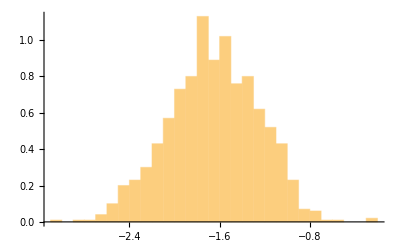

```mathematica
Histogram[sample,Automatic,"PDF"]
```

Sg process with adjusted  parameter values

```mathematica
sgProcNa=sgProc//.{delta->0.997,gamma->10,psi->1.1,rhoppbar->0.6,rhopbar->0.993,rhog->0.99}//.solP0
```

ARProcess[-0.00624,{0.99},0.000430589]

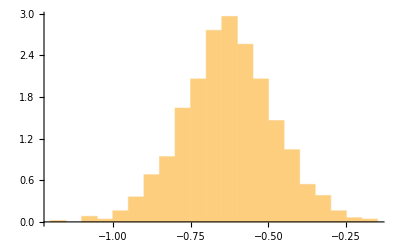

```mathematica
dataa=RandomFunction[sgProcNa,{1,500},1000];
samplea=dataa["SliceData",500];
Histogram[samplea,Automatic,"PDF"]
```

#### NRC - based on (un)conditional predictability of consumption growth with inflation

```mathematica
covdc12pilag = UncondCov[dc12,pi[t-1],m1]//.solP0;
covdcpilag = UncondCov[dc[t],pi[t-1],m1]//.solP0;
vpi=UncondVar[pi[t],m1]//.solP0;
```

```mathematica
beta12NRC=covdc12pilag/vpi
betaNRC=covdcpilag/vpi
```

-0.0909728

-0.349523

```mathematica
corrNRC = UncondCorr[dc12,pi[t-1],m1]//.solP0;
R2betaNRC = corrNRC^2
```

0.000204923

Above, both beta and R2 are very different from our draft, but that could be due to the new specification

Conditional slope

```mathematica
Cov[dc12,pi[t-1],t-2,m1]//Simplify
```

1/12 phip (phip rhocp+xic sg[-2+t])

```mathematica
covtdcpilag=Cov[dc[t],pi[t-1],t-2,m1]//.solP0
```

-3.15944×10^-7+0.000488262 sg[-2+t]

```mathematica
mcovtdcpilag=UncondE[covtdcpilag,m1]//.solP0
vcovtdcpilag=UncondVar[covtdcpilag,m1]//.solP0
```

-3.3627×10^-6

2.75745×10^-10

Something like confidence interval (plus/minus two standard deviation)

```mathematica
CIcovtdcpilagU=mcovtdcpilag+2*Sqrt[vcovtdcpilag]
CIcovtdcpilagL=mcovtdcpilag-2*Sqrt[vcovtdcpilag]
```

0.0000298484

-0.0000365738

#### Covariance of yields and stock returns

```mathematica
realNRC=UncondCov[bondyield[t,m],ret[t,1],m1]/UncondVar[bondyield[t,m],m1];
nomNRC=UncondCov[nombondyield[t,m],ret[t,1],m1]/UncondVar[nombondyield[t,m],m1];

yieldCurveNRC=Table[{m,realNRC},{m,1,120,12}];
nomYieldCurveNRC=Table[{m,nomNRC},{m,1,120,12}];
```

```mathematica
sol0 =m1["coeffsSolutionN"];
```

```mathematica
Manipulate[
sol=Quiet[
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500
]];
yc=ListLinePlot[yieldCurveNRC//.sol,PlotLegends->{"Real"}, PlotStyle->{Orange,Thick},AxesLabel->{"Maturity in months","Covariance/Variance"}];
nomyc=ListLinePlot[nomYieldCurveNRC//.sol,PlotLegends->{"Nominal"}, PlotStyle->{Darker[Green],Thick}];
Show[yc,nomyc,PlotRange->Full]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.01,0.01},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,yc,nomyc},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

#### Covariance of bond returns and stock returns

```mathematica
realNRC=UncondCov[bondret[t,m],ret[t,1],m1]/UncondVar[bondret[t,m],m1];
nomNRC=UncondCov[nombondret[t,m],ret[t,1],m1]/UncondVar[nombondret[t,m],m1];

yieldCurveNRC=Table[{m,realNRC},{m,1,120,12}];
nomYieldCurveNRC=Table[{m,nomNRC},{m,1,120,12}];
```

```mathematica
sol0 =m1["coeffsSolutionN"];
```

```mathematica
Manipulate[
sol=Quiet[
ToNum["Rules",
m1,
{delta->deltaM,Esg->EsgM,Esp->EspM,gamma->gammaM,muc->mucM,mupbar->mupbarM,phic->phicM,phig->phigM,phip->phipM,phipbarpb->phipbarpbM,phispw->phispwM,psi->psiM,rhocp->rhocpM,rhog->rhogM,rhopbar->rhopbarM,rhoppbar->rhoppbarM,vp->vpM,xic->xicM,xip->xipM},
sol0,
 MaxIterations->500
]];
yc=ListLinePlot[yieldCurveNRC//.sol,PlotLegends->{"Real"}, PlotStyle->{Orange,Thick},AxesLabel->{"Maturity in months","Covariance/Variance"}];
nomyc=ListLinePlot[nomYieldCurveNRC//.sol,PlotLegends->{"Nominal"}, PlotStyle->{Darker[Green],Thick}];
Show[yc,nomyc,PlotRange->Full]
,
{{deltaM,0.99},0.9,0.99999},{{EsgM,-0.00624},-0.01,0.01},{{EspM,0.00111},0.00000001,0.1},{{gammaM,15},1.5,75},{{mucM,0.0016426},0.0,0.01},{{mupbarM,0.00327532},0.0,0.05},{{phicM,0.00204654},-0.01,0.1},{{phigM,0.002927236529485},-0.01,0.1},{{phipM,-0.0024624},-0.01,0.1},{{phipbarpbM,1.5},0,7.5},{{phispwM,1.81*^-7},1.0*^-12,1.0*^-5},{{psiM,2},0.5,5},{{rhocpM,-0.0521066},-1,1},{{rhogM,0.996289},0.01,0.9999},{{rhopbarM,0.9},0.01,0.99999},{{rhoppbarM,0.5},0,2.5},{{vpM,0.979},0.01,0.99999},{{xicM,-0.198287},-1,1},{{xipM,0.00073007},0.00000001,0.05},
UnsavedVariables->{sol,yc,nomyc},SynchronousInitialization->False,SynchronousUpdating->False,ContinuousAction->False
]
```

### Extension 1: specification with stochastic volatility of inflation depending on inflation (vpp) and expected inflation (vppbar)

### Extension 2: specification with both NRC and stochastic volatility of inflation depending on inflation (rhogp, vpp) and expected inflation (rhogpbar, vppbar)